```mathematica
Maria José Domínguez 
Tarea #3
```

### 3.4.16

Como se tiene que -(∂V)/(∂x)= ẋ ⇒ V= -∫ẋ ⅆx, entonces, integrando para cada sistema dado y graficando r vs V y x vs V se puede ver como los puntos fijos estables del sistema corresponden a mínimos de potencial mientras que puntos fijos inestables corresponden a máximos:

a) ẋ=r-x.b2

```mathematica
Integrate[-(r-x^2),x]
V= -r*x+x^3/3
Manipulate[Show[Plot[-r*x+x^3/3,{x,-8,8},AxesLabel->{"x","V"}],Graphics[{PointSize[0.03], Point[{x,-r*x+x^3/3}/.Solve[-r*x+x^3/3==0,x, Reals], VertexColors->{Red, Green}]}],VectorPlot[{Sign[-r*x+x^3/3],0}, {x,-8,8},{y,-3,3},VectorStyle->{Gray,"Arrow"},VectorScale->0.1, RegionFunction->Function[{x,y,vx,vy,n}, -1<y<1] ]],{r,-10,10}]
```

-r x+x^3/3

-r x+x^3/3

x==0||x==-√3 √r||x==√3 √r

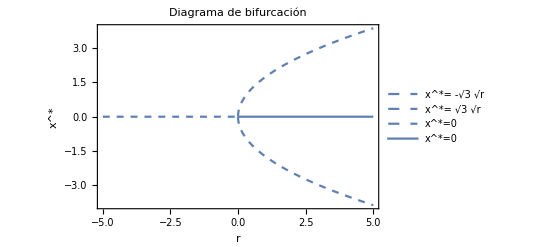

```mathematica
Reduce[-r*x+x^3/3==0,x]
f1[r_]:= -√3 √r
f2[r_]:= √3 √r
f3[r_]:= 0
F1= Plot[f1[r], {r,-5,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^*= -√3 √r"}, AxesLabel->{Style["r",20],Style["x^*",20]}];
F2=Plot[f2[r],{r,-5,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^*= √3 √r"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F3=Plot[f3[r],{r,-5,0},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^*=0"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F4=Plot[f3[r],{r,0,5},Frame->True, PlotRange->All, PlotStyle->Thick,PlotLegends->{"x^*=0"},AxesLabel->{Style["r",20],Style["x^*",20]}];
Show[F1,F2,F3,F4, PlotLabel-> "Diagrama de bifurcación"]
```

b) ẋ=rx-x.b2

```mathematica
Integrate[-(r*x-x^2),x]
V=-r*x^2/2+x^3/3
Manipulate[Show[Plot[-r*x^2/2+x^3/3,{x,-20,20},AxesLabel->{"x","V"}],Graphics[{PointSize[0.03], Point[{x,-r*x^2/2+x^3/3}/.Solve[-r*x^2/2+x^3/3==0,x, Reals], VertexColors->{Red, Green}]}],VectorPlot[{Sign[-r*x^2/2+x^3/3],0}, {x,-20,20},{y,-3,3},VectorStyle->{Gray,"Arrow"},VectorScale->0.1, RegionFunction->Function[{x,y,vx,vy,n}, -1<y<1] ]],{r,-10,10}]
```

-(r x^2)/2+x^3/3

-(r x^2)/2+x^3/3

x==0||x==(3 r)/2

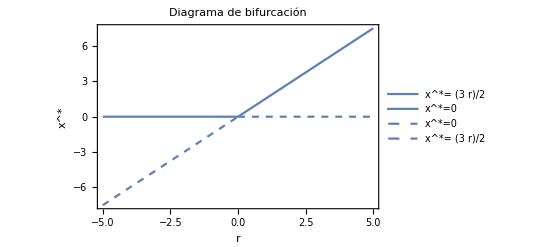

```mathematica
Reduce[-r*x^2/2+x^3/3==0,x]
f1[r_]:= (3 r)/2
f2[r_]:= 0
F1= Plot[f1[r], {r,0,5},Frame->True, PlotRange->All, PlotStyle->Thick,PlotLegends->{"x^*= (3 r)/2"}, AxesLabel->{Style["r",20],Style["x^*",20]}];
F2=Plot[f2[r],{r,-5,0},Frame->True, PlotRange->All, PlotStyle->Thick,PlotLegends->{"x^*=0"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F3=Plot[f2[r],{r,0,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^*=0"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F4= Plot[f1[r], {r,-5,0},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^*= (3 r)/2"}, AxesLabel->{Style["r",20],Style["x^*",20]}];
Show[F1,F2,F3,F4, PlotLabel-> "Diagrama de bifurcación"]
```

c) ẋ=rx+x.b3-x⁵

```mathematica
Integrate[-(r*x+x^3-x^5),x]
V=-r*x^2/2-x^4/4+x^6/6
Manipulate[Show[Plot[-r*x^2/2-x^4/4+x^6/6,{x,-5,5},AxesLabel->{"x","V"}],Graphics[{PointSize[0.03], Point[{x,-r*x^2/2-x^4/4+x^6/6}/.Solve[-r*x^2/2-x^4/4+x^6/6==0,x, Reals], VertexColors->{Red, Green}]}],VectorPlot[{Sign[-r*x^2/2-x^4/4+x^6/6],0}, {x,-5,5},{y,-3,3},VectorStyle->{Gray,"Arrow"},VectorScale->0.1, RegionFunction->Function[{x,y,vx,vy,n}, -1<y<1] ]],{r,-10,10}]
```

```mathematica
Reduce[-r*x^2/2-x^4/4+x^6/6==0,x]
f5[r_]:=0
f6[r_]:= -1/2 √(3-√3 √(3+16 r))
f7[r_]:=1/2 √(3-√3 √(3+16 r))
f8[r_]:=-1/2 √(3+√3 √(3+16 r))
f9[r_]:=1/2 √(3+√3 √(3+16 r))
F5=Plot[f5[r],{r,0,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^* = 0"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F6=Plot[f6[r],{r,-5,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^* = -1/2 √(3 - SqrtBox[3] SqrtBox[3 + 16 r])"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F7=Plot[f7[r],{r,-5,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^* = 1/2 √(3 - SqrtBox[3] SqrtBox[3 + 16 r])"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F8=Plot[f8[r],{r,-5,5},Frame->True, PlotRange->All, PlotStyle->Thick,PlotLegends->{"x^* = -1/2 √(3 + SqrtBox[3] SqrtBox[3 + 16 r])"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F9=Plot[f9[r],{r,-5,5},Frame->True, PlotRange->All, PlotStyle->Thick,PlotLegends->{"x^* = 1/2 √(3 + SqrtBox[3] SqrtBox[3 + 16 r])"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F10= Plot[f5[r],{r,-5,0},Frame->True, PlotRange->All, PlotStyle->Thick,PlotLegends->{"x^* = 0"},AxesLabel->{Style["r",20],Style["x^*",20]}];
Show[F5,F6,F7,F8,F9,F10, PlotLabel-> "Diagrama de bifurcación"]
```

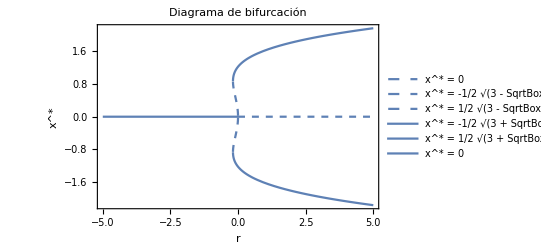

```mathematica
c
```

### 3.7.6

ẋ=-kxy
ẏ=kxy-ly
ż=ly

a) Haciendo N=x+y+z y derivando con respecto a t se tiene que Ṅ= ẋ + ẏ+ż= -kxy+kxy-ly+ly=0, entonces N es constante  .
b) ż=ly ⇒ y=(ż)/l, sustituyendo en ẋ:
dx/dt= - k/lx dz/dt ⇒ ∫_x_0^x 1/x ⅆx= -k/lz(t) ⇒ x(t)= x_0 ⅇ^(-k/l z(t))
c) Como N=x+y+z ⇒ y=N-x-z, reemplazando en ż:
ż= l[N-x-z], pero de b) se tiene que x= x_0 ⅇ^(-k/l z(t)) ⇒ ż= l[N-z-x_0 ⅇ^(-k/l z(t))]
d) Haciendo u=kz/l ⇒ u̇= k/l ż ⇒ ż= l/ku̇, reemplazando en ż= l[N-z-x_0 ⅇ^(-k/l z(t))]:
u̇ =k[N- l/k u-x_0 ⅇ^-u]
haciendo τ= 1/kx_0t ⇒ du/dτ= N/x_0- l/kx_0u- ⅇ^-u
haciendo ahora a= N/x_0 y b= l/kx_0 se tiene que:
du/dτ=a-bu-ⅇ^-u
e) Como k y l son constantes positivas y no puede haber un numero negativo de personas sanas, entonces x_0también es positivo, entonces, por deficinion b=l/kx_0>0.
analogamente, como x,y y z representan una población, estos no pueden tomar valores negativos, luego:
a=N/x_0=(x+y+z)/x_0, el menor valor se obtiene para x=x_0, y=y_0, z=z_0
⇒ a_min= (x_0+y_0+z_0)/x_0=x_0/x_0+y_0/x_0+z_0/x_0=1+y_0/x_0+z_0/x_0 ,luego, el valor mínimo es al menos 1 => a⩾1
f) graficando a-bu vs ⅇ^-u para u>0, a⩾1 y b>0 podemos ver que se interceptan en un sólo punto, el cual corresponde al punto fijo u*, para ver su estabilidad analizamos d/du[a-bu-ⅇ^-u]=-u+ⅇ^-u, como u>ⅇ^-u ⇒ -u+ⅇ^-u<0 y se tiene que el punto fijo es estable para todo u.
g) como  ż= l/ku̇ ⇒  z^(..)= l/ku^(..) y se tiene que el máximo para u̇ ocurre al mismo tiempo que para ż, ahora, como  ż=ly ⇒ z^(..)=lẏ y se tiene que si z^(..)=0 entonces ẏ=0
h) derivando se tiene que:
(d u̇)/dt= 1/(x_0.b2k.b2) (d.b2u)/(dτ.b2)= 1/(x_0.b2k.b2)(-b du/dτ-du/dτⅇ^-u)
⇒ (d u̇)/dt=1/(x_0.b2k.b2)(-b-ⅇ^-u)(a-bu-ⅇ^-u)
evaluendo en t=0:
(d u̇)/dt|_(t=0)=1/(x_0.b2k.b2)(-b-ⅇ^-u_0)(a-bu_0 -ⅇ^-u_0)= 1/(x_0.b2k.b2)(-b-ⅇ^-u_0)du/dτ|_(τ=0)
como u* es un punto fijo estable se sigue que du/dτ>0, y como ⅇ^-u_0⩽1 se sigue que si b<1 entonces (d u̇)/dt|_(t=0)>0
i) en este cado se tiene que (d u̇)/dt|_(t=0)<0 entonces el valor máximo ocurre en t=0. cuando t→∞ se tiene (d u̇)/dt=0 pues el sistema va hacia el punto de equiibrio.

```mathematica
Manipulate[Show[Plot[Exp[-u],{u,0,10}], Plot[a-b*u,{u,0,10}]],{a,1,20},{b,0,20}]
```

### 5.1.4

ẋ=3x-2y
ẏ=2y-x

En forma matricial ⇒ (ẋ
ẏ)=(3 | -2
-1 | 2) (x
y)

### 5.1.7

ẋ=x
ẏ=x+y

Al hallar los autovalores de la matriz de coeficientes vemos que ambos son reales positivos, por lo cual se tiene un nodo inestable. En el diagrama de fase podemos ver que (0,0) es el nodo, además de las trayectorias en azul y el flujo en rojo.

{1,1}

{{x→Function[{t},ⅇ^t C[1]],y→Function[{t},ⅇ^t t C[1]+ⅇ^t C[2]]}}

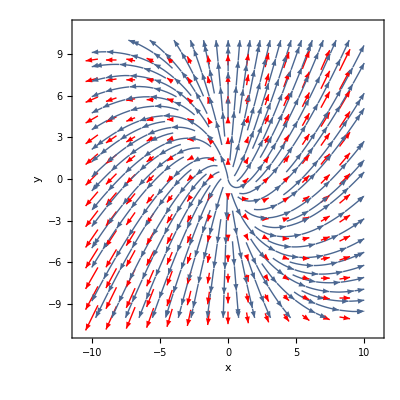

```mathematica
A={{1,0},{1,1}};
Eigenvalues[A]
X[t_]={x[t],y[t]};
sis1=X'[t]==A.X[t];
sol1=DSolve[sis1,{x,y},t]
Show[VectorPlot[{x,x+y},{x,-10,10},{y,-10,10}, VectorStyle->Red,StreamPoints->Automatic, FrameLabel->{Style["x",Italic],Style["y",Italic]}]]
```

### 5.1.9

ẋ=-y
ẏ=-x

a) En la gráfica vemos el flujo en rojo y las trayectorias en azul, además de que (0,0) corresponde a un punto de silla, hecho comprobado al hallar los autovalores y ver que son reales de signo opuesto.
b) Multiplicando x ẋ ⇒ xẋ= -yx=(-y)(-ẏ)=yẏ ⇒ ẋx-ẏy=0  ⇒ xdx-ydy=0 integrando:
∫xⅆx-∫yⅆy=0 ⇒ 1/2 x.b2-1/2y.b2 +c=0 ⇒ x.b2-y.b2=c lo cual corresponde a una familia de hiperbolas.
c) Al hallar los autovectores vemos que x+y=0 y -x+y=0 corresponden a las ecuaciones de las variedades estable e inestable del punto de silla, respectivamente.
d) Haciendo:
 u=x+y  ⇒ x=u-y (1)
 v=x-y (2)
sustituyendo 1 en 2:
v=u-2y ⇒ y= (u-v)/2 (3)
sustituyendo (3) en (1):
x=u-(u-v)/2= (u+v)/2
⇒ u̇+v̇=v-u 
    u̇-v̇=-v-u
 ⇒  u̇=-u
      v̇=v
 resolviendo (bajo la gráfica): 
 u= ⅇ^-t C[1]
v=ⅇ^t C[2]
 e) Por c) identificamos a u=0 como la ecuacion de la variedad estable y -v=0 de la variedad inestable
 f) Para (x_0,y_0):
u= u_0 ⅇ^-t 
v=v_0 ⅇ^t 
sustituyendo en x y y:
x= (u_0 ⅇ^-t+v_0 ⅇ^t)/2 ⇒ x= ((x_0+y_0)ⅇ^-t+(x_0-y_0)ⅇ^t)/2 
y= (u_0 ⅇ^-t-v_0 ⅇ^t)/2 ⇒ y= ((x_0+y_0)ⅇ^-t-(x_0-y_0)ⅇ^t)/2

{-1,1}

{{1,1},{-1,1}}

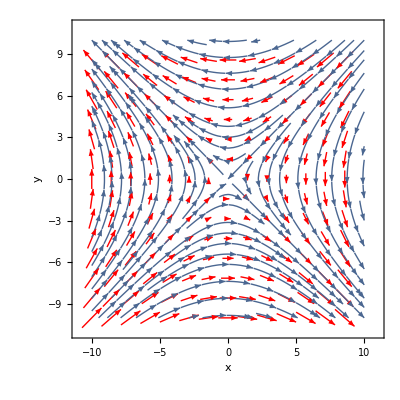

```mathematica
B={{0,-1},{-1,0}};
Eigenvalues[B]
Eigenvectors[B]
X[t_]={x[t],y[t]};
sis1=X'[t]==B.X[t];
sol1=DSolve[sis1,{x,y},t];
Show[VectorPlot[{-y,-x},{x,-10,10},{y,-10,10}, VectorStyle->Red,StreamPoints->Automatic, FrameLabel->{Style["x",Italic],Style["y",Italic]}]]
```

```mathematica
B1={{-1,0},{0,1}};
X[t_]={u[t],v[t]};
sis1=X'[t]==B1.X[t];
sol1=DSolve[sis1,{u,v},t]
```

{{u→Function[{t},ⅇ^-t C[1]],v→Function[{t},ⅇ^t C[2]]}}

### 5.2.1

ẋ=4x-y
ẏ=2x+y

a) (ẋ
ẏ)=(4 | -1
2 | 1) (x
y), tomando z como lamba vemos que el polinomio característico es 6-5 z+z^2 con autovalores z_1=3 y z_2=2
b) la solucion general está dada por:
x=ⅇ^(2 t) (-1+2 ⅇ^t) C[1]-ⅇ^(2 t) (-1+ⅇ^t) C[2]
y=2 ⅇ^(2 t) (-1+ⅇ^t) C[1]-ⅇ^(2 t) (-2+ⅇ^t) C[2]
c) como los autovalores son reales positivos (0,0) es un nodo inestable.
d) para x(0)=3 y y(0)=4:
x=ⅇ^(2 t) (1+2 ⅇ^t)
y=2 ⅇ^(2 t) (1+ⅇ^t)

```mathematica
A1={{4,-1},{2,1}};
Eigenvalues[A1]
CharacteristicPolynomial[A1,z]
X[t_]={x[t],y[t]};
sis1=X'[t]==A1.X[t];
sol1=DSolve[sis1,{x,y},t]
```

{3,2}

6-5 z+z^2

{{x→Function[{t},ⅇ^(2 t) (-1+2 ⅇ^t) C[1]-ⅇ^(2 t) (-1+ⅇ^t) C[2]],y→Function[{t},2 ⅇ^(2 t) (-1+ⅇ^t) C[1]-ⅇ^(2 t) (-2+ⅇ^t) C[2]]}}

```mathematica
solu= DSolve[{x'[t]==4*x[t]-y[t], y'[t]==2*x[t]+y[t],x[0]==3,y[0]==4},{x,y},{t,0,Infinity}]
```

{{x→Function[{t},ⅇ^(2 t) (1+2 ⅇ^t)],y→Function[{t},2 ⅇ^(2 t) (1+ⅇ^t)]}}

### 5.2.2

ẋ=x-y
ẏ=x+y

a) la matriz de coeficientes es A=(1 | -1
1 | 1),  su polinomio caracteristico es 2-2 λ+λ^2 y sus autovalores son λ_1=1+ⅈ y λ_2=1-ⅈ y autovectores asociados v_1=[ⅈ,1], v_2=[-ⅈ,1]
b) la solución en términos de funciones reales está dada por: 
x=ⅇ^t C[1] Cos[t]-ⅇ^t C[2] Sin[t]
y=ⅇ^t C[2] Cos[t]+ⅇ^t C[1] Sin[t]

```mathematica
A2={{1,-1},{1,1}};
Eigenvalues[A2]
Eigenvectors[A2]
CharacteristicPolynomial[A2,λ]
X[t_]={x[t],y[t]};
sis1=X'[t]==A2.X[t];
sol1=DSolve[sis1,{x,y},t]
```

{1+ⅈ,1-ⅈ}

{{ⅈ,1},{-ⅈ,1}}

2-2 λ+λ^2

{{x→Function[{t},ⅇ^t C[1] Cos[t]-ⅇ^t C[2] Sin[t]],y→Function[{t},ⅇ^t C[2] Cos[t]+ⅇ^t C[1] Sin[t]]}}

### 5.2.7

ẋ=5x+2y
ẏ=4x-3y

Como los autovalores son reales y de signo opuesto se tiene que (0,0) es un punto de silla, en el retrato de fase se observan los autovectores en naranja.

{1+2 √6,1-2 √6}

{{1/2 (2+√6),1},{1/2 (2-√6),1}}

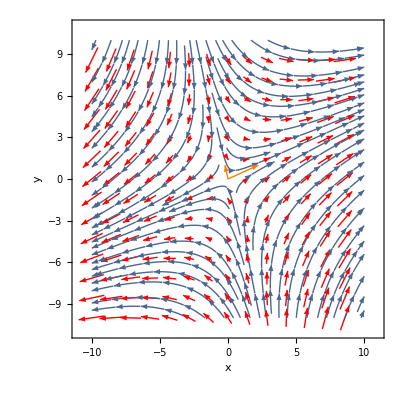

```mathematica
B2={{5,2},{4,-3}};
Eigenvalues[B2]
Eigenvectors[B2]
X[t_]={x[t],y[t]};
sis1=X'[t]==B2.X[t];
sol1=DSolve[sis1,{x,y},t];
v1={Arrowheads[Small],Arrow[{{0,0},{1/2 (2+√6),1}}]};
v2={Arrowheads[Small],Arrow[{{0,0},{1/2 (2-√6),1}}]};
Show[VectorPlot[{5*x+2*y,4*x-3*y},{x,-10,10},{y,-10,10}, VectorStyle->Red,StreamPoints->Automatic, FrameLabel->{Style["x",Italic],Style["y",Italic]}],Graphics[{Orange,v1}],Graphics[{Orange,v2}]]
```

### 5.2.14

A continuacion se pueden observar los posibles tipos de puntos críticos para una sistema  (ẋ
ẏ)=(a | b
c | d) (x
y) según varian los valores de a,b,c,d entre [-1,1]

```mathematica
Manipulate[
{evals,evecs}=Eigensystem[({{a, b}, {c, d}})];GraphicsColumn[{Show[StreamPlot[({{a, b}, {c, d}}).{x,y},{x,-1,1},{y,-1,1},Axes->True,StreamStyle->Thickness[Medium],PerformanceGoal->"Quality",StreamScale->Large,StreamPoints-> ControlActive[.5{{-1,1},{1,1},{1,-1},{-1,-1}},Coarse],Frame->False,Ticks->None],If[evecs==Re[evecs],ParametricPlot[Evaluate[t evecs],{t,-3,3},PlotStyle->{{Thick,RGBColor[0.5, 0.21, 0.36]}}],{}],PlotRange->1,ImageSize->{275,275}]}],
Row[{Spacer[60],Dynamic[Style[Text@TraditionalForm[HoldForm[({{ẋ}, {ẏ}})==Dynamic[({{a, b}, {c, d}})]({{x}, {y}})]],Medium]]}],Delimiter,
{{a,-1,Style["a_11",Medium]},-1,1,.01,Appearance->"Labeled"},
{{b,1,Style["a_12",Medium]},-1,1,.01,Appearance->"Labeled"},
{{c,.5,Style["a_21",Medium]},-1,1,.01,Appearance->"Labeled"},
{{d,-1,Style["a_22",Medium]},-1,1,.01,Appearance->"Labeled"},
{evecs,0,1,ControlType->None},
{evals,0,1,ControlType->None},Dynamic[Graphics[{PointSize[.04],RGBColor[0.5, 0.21, 0.36],Point[{Re[#],Im[#]}]&/@evals},PlotRange->{{-3,3},{-2,2}},Axes->True,AxesLabel->Text/@{Re[z],Im[z]},Ticks->None,ImagePadding->33,ImageSize->250,PlotLabel->Text@"\nAutovalores"]],
ControlPlacement->Left,AutorunSequencing->{1,2,3,4}]
```